```mathematica
ParametricPlot[{{-1+Cos[t],Sin[t]},{+1+Cos[t]/2,Sin[t]/2}},{t,0,2Pi}]
```

```mathematica
f[x_,y_,n_,d_]:=Join[Table[{Abs[x-Cos[t]i/(n d)],Abs[y-Sin[t]i/(n d)]},{i,1,n-1}]]
```

```mathematica
c[n_]:=Join[{Cycles[{}]},Table[Cycles[{{i,i+1}}],{i,1,n-1}]]
```

```mathematica
c[5]
```

{Cycles[{}],Cycles[{{1,2}}],Cycles[{{2,3}}],Cycles[{{3,4}}],Cycles[{{4,5}}]}

```mathematica
pa[n_]:=Table[Table[1,{i,1,n}]+PadLeft[IntegerDigits[x,n],n],{x,1,n^n-1}]
```

```mathematica
pa[3]
```

{{1,1,1,2},{2,1,1,3},{3,1,2,1},{4,1,2,2},{5,1,2,3},{6,1,3,1},{7,1,3,2},{8,1,3,3},{9,2,1,1},{10,2,1,2},{11,2,1,3},{12,2,2,1},{13,2,2,2},{14,2,2,3},{15,2,3,1},{16,2,3,2},{17,2,3,3},{18,3,1,1},{19,3,1,2},{20,3,1,3},{21,3,2,1},{22,3,2,2},{23,3,2,3},{24,3,3,1},{25,3,3,2},{26,3,3,3}}

```mathematica
ta[x_,n_]:=IdentityMatrix[n]+SparseArray[{{x,x+1},{x+1,x},{x,x},{x+1,x+1}}->{1,1,-1,-1},{n,n}]
```

```mathematica
ta[3,4].ta[2,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0)

```mathematica
t[n_]:=Join[{IdentityMatrix[n]},Table[ta[x,n],{x,1,n-1}]]
```

```mathematica
Map[MatrixForm,t[3]]
```

```mathematica
Apply[Dot,{({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}),({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}),({{1, 0, 0}, {0, 0, 1}, {0, 1, 0}})}]
```

{{0,0,1},{1,0,0},{0,1,0}}

```mathematica
p[n_]:=Map[t[n][[Delete[#,1]]]&,pa[n]]
```

```mathematica
Length[p[3]]
```

26

```mathematica
q=Table[Apply[Dot,Delete[p[3][[i]],1]],{i,1,3^3-1}]
```

{{{0,1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}}}

```mathematica
Map[FromDigits[Flatten[#],2]&,q,2]
```

```mathematica
Length[{17,20,21,17,20,21,17,20,21,17,20,21,17,20,21,17,20,21,17,20,21,17,20,21,17,20}]
```

26

```mathematica
f[n_]:=Map[FromDigits[Flatten[#],2]&,Table[Apply[Dot,Delete[p[n][[i]],1]],{i,1,n^n-1}]]
```

```mathematica
f[3]
```

```mathematica
w=4;
ww=f[w]
Flatten[Map[First,Table[Position[ww,i],{i,DeleteDuplicates[ww]}]]]
```

{18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825,33825,18465,33345,33810,18465,33825,10305,18450,33345,17025,33825,33090,33810,18450,33300,33825}

{1,2,3,5,6,7,9,11,14}

```mathematica
w=5;
ww=f[w]
Flatten[Map[First,Table[Position[ww,i],{i,DeleteDuplicates[ww]}]]]
```

```mathematica
pa[n_]:=Table[Table[1,{i,1,n}]+PadLeft[IntegerDigits[x,n],n],{x,1,n^n-1}]
ta[x_,n_]:=IdentityMatrix[n]+SparseArray[{{x,x+1},{x+1,x},{x,x},{x+1,x+1}}->{1,1,-1,-1},{n,n}]
t[n_]:=Join[{IdentityMatrix[n]},Table[ta[x,n],{x,1,n-1}]]
p[n_]:=Map[t[n][[Delete[#,1]]]&,pa[n]]
f[n_]:=Map[FromDigits[Flatten[#],2]&,Table[Apply[Dot,Delete[p[n][[k]],1]],{k,1,n^n-1}]]
w=6;
ww=f[w]
Monitor[Flatten[Map[First,Table[Position[ww,i],{i,DeleteDuplicates[ww]}]]],i]
```

```mathematica
SetAttributes[RemainingNonUniformTime,HoldAll];
RemainingNonUniformTime[content_,ticker_,min_,max_,period_]:=Block[{T0=AbsoluteTime[],lstTickerTracker,tickerTracker={}},ticker=min;
Monitor[content,Refresh[lstTickerTracker=AppendTo[tickerTracker,AbsoluteTime[]];
Panel@Grid[{{"Initiated at timestamp:",ToString[DateString[T0]]},{"Current progress:  ",ProgressIndicator[ticker,{min,max}],ticker},{"Avg. Exp. process termination: ",If[Length[lstTickerTracker]>9,ToString[DateString[(T0+(0.5*First@Commonest@Differences@lstTickerTracker/10*(max-min))+(0.5*Max@Differences@Take[lstTickerTracker,-10]/10*(max-min)))]],"Initializing..."]},{"Realtime prediction:  ",If[Length[lstTickerTracker]>9,ToString[DateString[(AbsoluteTime[]+(Mean@Differences@Take[lstTickerTracker,-10]/10)*(max-ticker))]],"Initializing..."]},{"Current timestamp: ",ToString[DateString[AbsoluteTime[]]]}},Alignment->Left],UpdateInterval->period,TrackedSymbols->{}]]]
```

```mathematica
ttt=t[6]
papa=pa[6]
```

{{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},{{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},{{1,0,0,0,0,0},{0,0,1,0,0,0},{0,1,0,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,0,1,0},{0,0,0,1,0,0},{0,0,0,0,0,1}},{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0}}}

```mathematica
ppp=Map[ttt[[Delete[#,1]]]&,papa]
```

```mathematica
Monitor[Map[FromDigits[Flatten[#],2]&,Table[Apply[Dot,Delete[ppp[[k]],1]],{k,1,6^6-1}]],k]
```

```mathematica
DeleteDuplicates[ww]
%//Length
```

98

```mathematica
qas=Table[Flatten[Position[ww,DeleteDuplicates[ww][[j]]]],{j,1,98}]
```

```mathematica
Max[qas]
```

```mathematica
Log[46655]/Log[2]//N
```

15.5097

```mathematica
Length[qas]
```

98

```mathematica
st[list_,z_]:=First[Sort[list[[z]],Apply[Plus,IntegerDigits[#1,2]]<Apply[Plus,IntegerDigits[#2,2]]&]]
```

```mathematica
st[qas]
```

```mathematica
a1={64,128,16385,256,4096,40960,512,513,8704,8200,32896,17416,32768,32,4608,8448,2048,32769,40961,10240,8256,37890,32772,16640,4224,33088,16386,32778,65,34816,8322,36865,32898,8328,8320,10242,36882,16448,16648,4609,8450,16392,25600,137,16384,33284,16449,4097,5130,18441,36872,32900,37892,37894,321,32775,32792,5120,4616,40976,8192,40977,34049,8194,32780,32793,8201,5121,8324,17413,32901,36873,32897,32902,8329,17414,2049,36886,17417,33034,36884,36897,24584,10251,4618,16393,40983,2120,2050,45062,2121,16769,16407,25609,1064,1066,24585,5132};
```

```mathematica
dd=Map[PadLeft[IntegerDigits[#,2],16]&,a1]
ss=Map[Flatten[Position[#,1]]&,dd]
Length[ss]
Sort[DeleteDuplicates[Flatten[ss]],Less]
```

98

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
M=Partition[Flatten[Table[Piecewise[{{Flatten[Position[ss,ss[[i]]∩ss[[j]]]], Flatten[Position[ss,ss[[i]]∩ss[[j]]]]≠{}}, {{0}, True}}],{i,1,98},{j,1,98}]],98];
M//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 45 | 0 | 0 | 45 | 45 | 0 | 45 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 3 | 0 | 0 | 0 | 45 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 3 | 0
0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 0 | 5 | 0 | 5 | 5 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 61 | 61 | 13 | 0 | 13 | 0 | 0 | 61 | 0 | 13 | 6 | 61 | 61 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 0 | 13 | 61 | 13 | 13 | 61 | 61 | 61 | 13 | 0 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 13 | 13 | 0 | 0 | 6 | 61 | 6 | 13 | 61 | 13 | 13 | 61 | 0 | 61 | 0 | 13 | 13 | 13 | 13 | 61 | 0 | 0 | 13 | 0 | 13 | 13 | 13 | 61 | 61 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 0 | 0 | 7 | 7 | 7 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 7 | 8 | 7 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 61 | 7 | 7 | 9 | 61 | 0 | 0 | 0 | 0 | 7 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 7 | 61 | 0 | 61 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 7 | 0 | 61 | 0 | 0 | 61 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 10 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 10 | 61 | 61 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 10 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 10 | 0 | 0 | 61 | 0 | 0 | 61 | 0 | 0 | 0 | 10 | 0 | 0 | 10 | 0
0 | 2 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 11 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 13 | 0 | 2 | 13 | 0 | 13 | 0 | 13 | 2 | 13 | 11 | 2 | 2 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 11 | 13 | 13 | 0 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 13 | 13 | 0 | 0 | 2 | 0 | 11 | 13 | 11 | 11 | 2 | 0 | 0 | 13 | 0 | 13 | 13 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 13 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 42 | 0 | 0 | 42 | 0 | 0 | 45 | 0 | 45 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 42 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 45 | 45 | 12 | 0 | 0 | 42 | 0
0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 0 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 13 | 13 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 14 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0 | 7 | 7 | 7 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 5 | 5 | 0 | 5 | 0 | 5 | 5 | 0 | 0 | 0 | 5 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 5 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 4 | 0 | 61 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 4 | 0 | 16 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 4 | 61 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 61 | 61 | 0 | 0 | 61 | 0 | 0 | 61 | 0 | 4 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 17 | 17 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 18 | 18 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 0 | 13 | 0 | 18 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 18 | 13 | 0 | 0 | 13 | 0 | 18 | 18 | 0 | 13 | 18 | 0 | 0 | 0 | 0 | 18 | 18 | 18 | 13 | 0 | 0 | 0 | 13 | 0 | 13 | 13 | 18 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 61 | 61 | 13 | 0 | 13 | 0 | 0 | 61 | 0 | 18 | 19 | 61 | 61 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 0 | 13 | 61 | 18 | 13 | 61 | 61 | 61 | 13 | 0 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 18 | 13 | 0 | 0 | 6 | 61 | 19 | 18 | 61 | 13 | 18 | 0 | 0 | 61 | 0 | 18 | 18 | 18 | 13 | 0 | 0 | 0 | 13 | 0 | 13 | 13 | 18 | 61 | 0 | 0 | 0 | 19 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 17 | 0 | 61 | 20 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 61 | 0 | 0 | 61 | 61 | 20 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 61 | 20 | 0 | 0 | 61 | 17 | 17 | 61 | 17 | 0 | 0 | 61 | 0 | 0 | 61 | 0
1 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 21 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 1 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 61 | 1 | 0 | 61 | 1 | 0 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 5 | 0 | 0 | 13 | 13 | 0 | 0 | 22 | 13 | 0 | 5 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 5 | 0 | 0 | 0 | 13 | 0 | 22 | 0 | 0 | 13 | 58 | 5 | 13 | 0 | 13 | 0 | 0 | 13 | 13 | 0 | 58 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58
0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 23 | 0 | 0 | 13 | 0 | 13 | 0 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 13 | 23 | 23 | 23 | 0 | 23 | 13 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 23 | 13 | 0 | 0 | 0 | 0 | 23 | 13 | 13 | 23 | 0 | 0 | 0 | 23 | 0 | 13 | 23 | 13 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 45 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 0 | 4 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 24 | 0 | 4 | 45 | 45 | 0 | 45 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 4 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 24 | 45 | 45 | 0 | 0 | 45 | 0
0 | 2 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 2 | 5 | 2 | 2 | 2 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 5 | 5 | 0 | 5 | 2 | 5 | 5 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 2 | 0 | 2 | 5 | 2 | 2 | 2 | 0 | 0 | 5 | 0 | 0 | 5 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 5
1 | 0 | 0 | 4 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 4 | 0 | 13 | 13 | 0 | 1 | 13 | 13 | 4 | 0 | 26 | 0 | 13 | 1 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 1 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 13 | 1 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 13 | 1 | 0 | 13 | 1 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 45 | 0 | 0 | 45 | 45 | 0 | 45 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 27 | 0 | 0 | 45 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 45 | 27 | 45 | 0 | 0 | 45 | 0
0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 13 | 0 | 28 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 28 | 13 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 17 | 13 | 13 | 17 | 0 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 0 | 30 | 0 | 13 | 13 | 0 | 0 | 17 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 17 | 13 | 13 | 13 | 13 | 0 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 0 | 17 | 13 | 0 | 13 | 13 | 13 | 0 | 17 | 0 | 0 | 13 | 17 | 17 | 13 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 2 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 31 | 0 | 0 | 35 | 35 | 64 | 0 | 0 | 0 | 0 | 64 | 0 | 61 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 64 | 0 | 0 | 61 | 0 | 35 | 0 | 2 | 0 | 2 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 64 | 0 | 0 | 64 | 0 | 0 | 64 | 0 | 2 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 5 | 0 | 0 | 18 | 18 | 0 | 0 | 0 | 13 | 0 | 5 | 13 | 0 | 13 | 0 | 13 | 0 | 32 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 48 | 5 | 0 | 0 | 13 | 0 | 0 | 0 | 18 | 13 | 5 | 5 | 13 | 0 | 18 | 18 | 0 | 13 | 18 | 0 | 48 | 0 | 0 | 18 | 32 | 18 | 13 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 32 | 0 | 0 | 5 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
0 | 2 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 11 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 2 | 13 | 0 | 0 | 0 | 13 | 0 | 13 | 33 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 11 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 13 | 13 | 0 | 0 | 2 | 0 | 11 | 13 | 11 | 33 | 2 | 0 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 10 | 2 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 35 | 0 | 2 | 34 | 35 | 61 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 10 | 0 | 35 | 0 | 2 | 0 | 2 | 2 | 34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 10 | 0 | 0 | 61 | 0 | 0 | 61 | 0 | 2 | 0 | 10 | 0 | 0 | 10 | 0
0 | 2 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 2 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 35 | 0 | 2 | 35 | 35 | 61 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 61 | 0 | 35 | 0 | 2 | 0 | 2 | 2 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 61 | 0 | 0 | 61 | 0 | 2 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 17 | 0 | 61 | 20 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 64 | 0 | 0 | 61 | 61 | 36 | 0 | 0 | 0 | 0 | 64 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 64 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 61 | 36 | 0 | 0 | 64 | 17 | 89 | 64 | 17 | 0 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 5 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 5 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 37 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 5 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 5 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 37 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
1 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 45 | 0 | 1 | 45 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 38 | 45 | 0 | 0 | 45 | 45 | 0 | 45 | 0 | 38 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 1 | 0 | 0 | 1 | 45 | 45 | 45 | 0 | 0 | 45 | 0
0 | 0 | 45 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 42 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 0 | 4 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 39 | 0 | 4 | 42 | 45 | 0 | 45 | 0 | 45 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 42 | 0 | 0 | 0 | 42 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 24 | 45 | 42 | 0 | 0 | 42 | 0
0 | 0 | 0 | 0 | 5 | 0 | 7 | 8 | 7 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 48 | 5 | 0 | 5 | 0 | 5 | 5 | 0 | 0 | 0 | 5 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 48 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 4 | 0 | 61 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 64 | 0 | 0 | 61 | 61 | 64 | 0 | 0 | 4 | 0 | 41 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 4 | 64 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 64 | 0 | 0 | 64 | 0 | 0 | 64 | 0 | 4 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 42 | 0 | 0 | 42 | 45 | 0 | 45 | 0 | 45 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 42 | 0 | 0 | 0 | 42 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 45 | 45 | 42 | 0 | 0 | 42 | 0
0 | 0 | 45 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 45 | 45 | 0 | 61 | 45 | 43 | 0 | 45 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 45 | 61 | 0 | 0 | 61 | 0 | 45 | 45 | 43 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 44 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 44 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 45 | 0 | 0 | 45 | 45 | 0 | 45 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 45 | 45 | 45 | 0 | 0 | 45 | 0
0 | 0 | 0 | 0 | 0 | 13 | 7 | 7 | 7 | 0 | 13 | 0 | 13 | 0 | 7 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 23 | 0 | 0 | 13 | 0 | 13 | 0 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 46 | 0 | 0 | 0 | 0 | 13 | 23 | 23 | 23 | 0 | 23 | 13 | 0 | 7 | 13 | 0 | 13 | 13 | 0 | 23 | 13 | 0 | 0 | 0 | 0 | 23 | 13 | 13 | 23 | 0 | 0 | 0 | 23 | 0 | 13 | 23 | 13 | 0 | 0 | 7 | 0 | 23 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 45 | 0 | 1 | 45 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 38 | 45 | 0 | 0 | 45 | 45 | 0 | 45 | 0 | 47 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 3 | 0 | 0 | 0 | 45 | 0 | 0 | 3 | 0 | 1 | 0 | 0 | 29 | 3 | 3 | 3 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 5 | 0 | 5 | 0 | 5 | 5 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 48 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 49 | 0 | 0 | 0 | 58 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 17 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 45 | 42 | 0 | 0 | 42 | 45 | 0 | 45 | 0 | 3 | 0 | 0 | 50 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 45 | 77 | 0 | 86 | 0 | 0 | 0 | 42 | 0 | 0 | 86 | 0 | 0 | 17 | 0 | 0 | 3 | 3 | 86 | 0 | 0 | 86 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 5 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 5 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 5 | 0 | 0 | 51 | 13 | 0 | 0 | 0 | 13 | 0 | 5 | 0 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 13 | 51 | 13 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 11 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 23 | 0 | 2 | 13 | 0 | 13 | 0 | 13 | 2 | 13 | 11 | 2 | 2 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 23 | 0 | 0 | 0 | 0 | 13 | 52 | 23 | 23 | 0 | 23 | 13 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 23 | 13 | 0 | 0 | 0 | 0 | 52 | 13 | 11 | 52 | 2 | 0 | 0 | 23 | 0 | 13 | 23 | 13 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 23 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 5 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 23 | 0 | 5 | 13 | 0 | 13 | 0 | 13 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 5 | 58 | 0 | 0 | 23 | 53 | 53 | 0 | 23 | 13 | 58 | 5 | 13 | 0 | 13 | 0 | 0 | 23 | 13 | 0 | 58 | 0 | 0 | 23 | 0 | 13 | 23 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 5 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 5 | 0 | 0 | 13 | 13 | 0 | 0 | 22 | 23 | 0 | 5 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 5 | 0 | 0 | 0 | 23 | 53 | 54 | 0 | 0 | 13 | 58 | 5 | 13 | 0 | 13 | 0 | 0 | 23 | 13 | 0 | 58 | 0 | 0 | 23 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 55 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 18 | 18 | 0 | 0 | 0 | 23 | 0 | 0 | 13 | 0 | 0 | 0 | 13 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 13 | 23 | 23 | 0 | 0 | 56 | 13 | 0 | 0 | 13 | 0 | 18 | 18 | 0 | 23 | 18 | 0 | 0 | 0 | 0 | 0 | 18 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23 | 18 | 0 | 0 | 0 | 0 | 56 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 0 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 0 | 13 | 57 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 57 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 58 | 0 | 5 | 0 | 58 | 58 | 0 | 0 | 0 | 58 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58
0 | 0 | 0 | 0 | 5 | 0 | 7 | 7 | 7 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 5 | 59 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 5 | 0 | 0 | 59 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 61 | 61 | 13 | 0 | 13 | 0 | 0 | 61 | 0 | 13 | 6 | 61 | 61 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 0 | 13 | 61 | 13 | 13 | 61 | 61 | 61 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 13 | 0 | 0 | 0 | 60 | 61 | 60 | 13 | 61 | 13 | 0 | 61 | 0 | 61 | 0 | 13 | 13 | 13 | 13 | 61 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 61 | 61 | 0 | 0 | 60 | 0 | 0 | 6 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 61 | 0 | 0 | 61 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 61 | 61 | 13 | 0 | 13 | 0 | 0 | 61 | 0 | 18 | 19 | 61 | 61 | 13 | 13 | 0 | 0 | 13 | 0 | 13 | 0 | 13 | 61 | 18 | 13 | 61 | 61 | 61 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 13 | 0 | 18 | 0 | 0 | 0 | 60 | 61 | 62 | 18 | 61 | 13 | 0 | 0 | 0 | 61 | 0 | 18 | 18 | 18 | 13 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 18 | 61 | 0 | 0 | 0 | 62 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 4 | 0 | 18 | 18 | 0 | 0 | 0 | 13 | 4 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 18 | 13 | 0 | 0 | 0 | 13 | 0 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 18 | 13 | 0 | 0 | 13 | 0 | 18 | 63 | 0 | 13 | 18 | 0 | 0 | 0 | 0 | 18 | 18 | 18 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 13 | 18 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 64 | 0 | 0 | 61 | 61 | 64 | 0 | 0 | 0 | 0 | 64 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 64 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 64 | 0 | 0 | 64 | 0 | 0 | 64 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 23 | 0 | 0 | 13 | 0 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 23 | 23 | 23 | 0 | 23 | 0 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 65 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 13 | 23 | 0 | 0 | 0 | 23 | 0 | 0 | 23 | 13 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 18 | 18 | 0 | 0 | 13 | 13 | 0 | 0 | 13 | 0 | 0 | 0 | 13 | 0 | 18 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 13 | 13 | 13 | 0 | 18 | 57 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 66 | 0 | 0 | 0 | 0 | 18 | 0 | 18 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 10 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 10 | 61 | 61 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 61 | 0 | 0 | 67 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 67 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 67 | 0 | 0 | 67 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 58 | 0 | 5 | 0 | 58 | 58 | 0 | 0 | 0 | 58 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 68 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 48 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58
0 | 2 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 2 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 35 | 0 | 2 | 35 | 35 | 61 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 61 | 0 | 69 | 0 | 0 | 0 | 2 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 61 | 0 | 0 | 61 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 45 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 70 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0
0 | 2 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 11 | 0 | 13 | 0 | 0 | 0 | 0 | 18 | 18 | 0 | 0 | 13 | 23 | 0 | 2 | 13 | 0 | 13 | 0 | 13 | 2 | 18 | 11 | 2 | 2 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 13 | 52 | 23 | 23 | 0 | 0 | 13 | 0 | 0 | 13 | 0 | 18 | 18 | 0 | 23 | 18 | 0 | 0 | 0 | 0 | 71 | 18 | 73 | 52 | 0 | 0 | 0 | 23 | 0 | 13 | 23 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 5 | 0 | 0 | 18 | 18 | 0 | 0 | 0 | 13 | 0 | 5 | 13 | 0 | 0 | 0 | 13 | 0 | 32 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 48 | 0 | 0 | 51 | 13 | 0 | 0 | 0 | 18 | 0 | 5 | 0 | 13 | 0 | 18 | 18 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 18 | 72 | 18 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 11 | 0 | 13 | 0 | 0 | 0 | 0 | 18 | 18 | 0 | 0 | 13 | 13 | 0 | 2 | 13 | 0 | 13 | 0 | 13 | 2 | 18 | 11 | 2 | 2 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 11 | 13 | 13 | 0 | 18 | 13 | 0 | 0 | 13 | 0 | 18 | 18 | 0 | 13 | 18 | 0 | 0 | 2 | 0 | 73 | 18 | 73 | 11 | 0 | 0 | 0 | 13 | 0 | 13 | 13 | 18 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 11 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 23 | 0 | 2 | 13 | 0 | 0 | 0 | 13 | 0 | 13 | 33 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 23 | 0 | 0 | 0 | 0 | 13 | 52 | 23 | 0 | 0 | 0 | 13 | 0 | 0 | 13 | 0 | 13 | 13 | 0 | 23 | 13 | 0 | 0 | 0 | 0 | 52 | 13 | 11 | 74 | 2 | 0 | 0 | 0 | 0 | 0 | 23 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 10 | 2 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 35 | 0 | 2 | 34 | 35 | 61 | 0 | 0 | 0 | 0 | 61 | 0 | 61 | 44 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 61 | 0 | 0 | 67 | 0 | 35 | 0 | 0 | 0 | 0 | 2 | 75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 67 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 67 | 0 | 0 | 67 | 0
0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 45 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 76 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 45 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 77 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 77 | 0 | 0 | 0 | 0 | 0 | 0 | 77 | 0 | 0 | 0 | 17 | 17 | 0 | 77 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 5 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 23 | 0 | 5 | 13 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 37 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 5 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 13 | 0 | 23 | 0 | 0 | 5 | 0 | 0 | 23 | 0 | 13 | 0 | 0 | 0 | 0 | 78 | 0 | 0 | 81 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 42 | 0 | 0 | 42 | 0 | 0 | 45 | 0 | 3 | 0 | 0 | 86 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 79 | 0 | 0 | 0 | 42 | 0 | 0 | 86 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 79 | 0 | 0 | 86 | 0
0 | 0 | 0 | 4 | 0 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 4 | 0 | 13 | 13 | 0 | 0 | 0 | 13 | 4 | 0 | 0 | 0 | 28 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 13 | 13 | 0 | 4 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 80 | 13 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 0 | 5 | 0 | 0 | 13 | 13 | 0 | 0 | 0 | 23 | 0 | 5 | 13 | 0 | 13 | 0 | 13 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 5 | 5 | 0 | 0 | 23 | 0 | 0 | 0 | 23 | 0 | 5 | 5 | 0 | 0 | 0 | 13 | 0 | 23 | 0 | 0 | 5 | 0 | 0 | 23 | 0 | 13 | 23 | 0 | 0 | 0 | 81 | 0 | 13 | 81 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 13 | 0 | 0 | 0 | 0 | 13 | 0 | 13 | 14 | 5 | 0 | 0 | 18 | 18 | 0 | 0 | 0 | 13 | 0 | 5 | 13 | 0 | 13 | 0 | 13 | 0 | 32 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 48 | 5 | 0 | 0 | 13 | 0 | 0 | 0 | 18 | 13 | 5 | 5 | 13 | 0 | 18 | 18 | 0 | 13 | 18 | 0 | 48 | 0 | 0 | 18 | 32 | 18 | 13 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 82 | 0 | 0 | 5 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 14 | 0 | 5
0 | 0 | 45 | 0 | 0 | 61 | 0 | 0 | 61 | 10 | 0 | 42 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 61 | 61 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 61 | 0 | 0 | 10 | 61 | 61 | 0 | 45 | 42 | 0 | 61 | 42 | 0 | 0 | 45 | 0 | 45 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 61 | 0 | 61 | 0 | 0 | 10 | 0 | 61 | 45 | 0 | 0 | 0 | 0 | 10 | 45 | 0 | 0 | 42 | 0 | 0 | 0 | 83 | 10 | 0 | 42 | 61 | 0 | 0 | 61 | 0 | 45 | 45 | 83 | 0 | 0 | 83 | 0
0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 10 | 0 | 0 | 0 | 0 | 0 | 61 | 17 | 0 | 0 | 20 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 64 | 0 | 0 | 10 | 61 | 36 | 0 | 0 | 0 | 0 | 64 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 64 | 0 | 0 | 67 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 77 | 0 | 0 | 0 | 0 | 0 | 10 | 84 | 0 | 0 | 0 | 0 | 89 | 64 | 0 | 0 | 0 | 67 | 0 | 0 | 67 | 0
0 | 0 | 0 | 0 | 5 | 0 | 7 | 7 | 7 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 59 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 85 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 42 | 0 | 0 | 42 | 45 | 0 | 45 | 0 | 3 | 0 | 0 | 86 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 86 | 0 | 0 | 0 | 42 | 0 | 0 | 86 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 86 | 0 | 0 | 86 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 61 | 61 | 13 | 0 | 13 | 0 | 0 | 61 | 0 | 18 | 19 | 61 | 61 | 0 | 23 | 0 | 0 | 13 | 0 | 0 | 0 | 13 | 64 | 18 | 0 | 61 | 61 | 64 | 0 | 0 | 0 | 0 | 64 | 0 | 61 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 13 | 23 | 23 | 0 | 0 | 56 | 0 | 0 | 0 | 60 | 61 | 62 | 18 | 64 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 61 | 0 | 0 | 0 | 87 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 17 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 17 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 88 | 17 | 0 | 88 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 89 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 89 | 0 | 0 | 0 | 17 | 89 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 6 | 0 | 0 | 61 | 61 | 13 | 0 | 13 | 0 | 5 | 61 | 0 | 13 | 6 | 61 | 61 | 0 | 23 | 0 | 5 | 13 | 0 | 0 | 0 | 13 | 64 | 0 | 0 | 61 | 61 | 64 | 0 | 0 | 0 | 5 | 64 | 0 | 61 | 0 | 0 | 23 | 0 | 5 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 13 | 5 | 5 | 6 | 61 | 6 | 13 | 64 | 23 | 13 | 61 | 5 | 0 | 0 | 23 | 0 | 13 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 64 | 0 | 0 | 0 | 0 | 0 | 90 | 0 | 0 | 0 | 61 | 0 | 0 | 61 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 17 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 29 | 17 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 77 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 88 | 17 | 0 | 91 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 3 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 45 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 2 | 4 | 45 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 45 | 24 | 0 | 4 | 45 | 45 | 0 | 45 | 0 | 3 | 0 | 0 | 3 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 3 | 0 | 0 | 0 | 2 | 0 | 45 | 0 | 0 | 3 | 4 | 0 | 0 | 45 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 92 | 3 | 3 | 0 | 0 | 3 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 45 | 0 | 0 | 45 | 45 | 0 | 45 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 45 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 93 | 3 | 0 | 0 | 3 | 0
0 | 0 | 3 | 0 | 0 | 61 | 0 | 0 | 61 | 10 | 0 | 12 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 61 | 0 | 0 | 10 | 61 | 61 | 0 | 45 | 42 | 0 | 61 | 42 | 43 | 0 | 45 | 0 | 3 | 0 | 0 | 86 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 61 | 0 | 0 | 67 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 79 | 0 | 0 | 0 | 83 | 67 | 0 | 86 | 0 | 0 | 0 | 61 | 0 | 3 | 3 | 94 | 0 | 0 | 97 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 95 | 95 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 95 | 96 | 0 | 0
0 | 0 | 3 | 0 | 0 | 61 | 0 | 0 | 61 | 10 | 0 | 42 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 45 | 0 | 0 | 45 | 0 | 0 | 0 | 61 | 0 | 0 | 10 | 61 | 61 | 0 | 45 | 42 | 0 | 61 | 42 | 0 | 0 | 45 | 0 | 3 | 0 | 0 | 86 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 61 | 0 | 0 | 61 | 0 | 0 | 67 | 0 | 61 | 3 | 0 | 0 | 0 | 0 | 67 | 45 | 0 | 0 | 86 | 0 | 0 | 0 | 83 | 67 | 0 | 86 | 0 | 0 | 0 | 61 | 0 | 3 | 3 | 97 | 0 | 0 | 97 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 98)

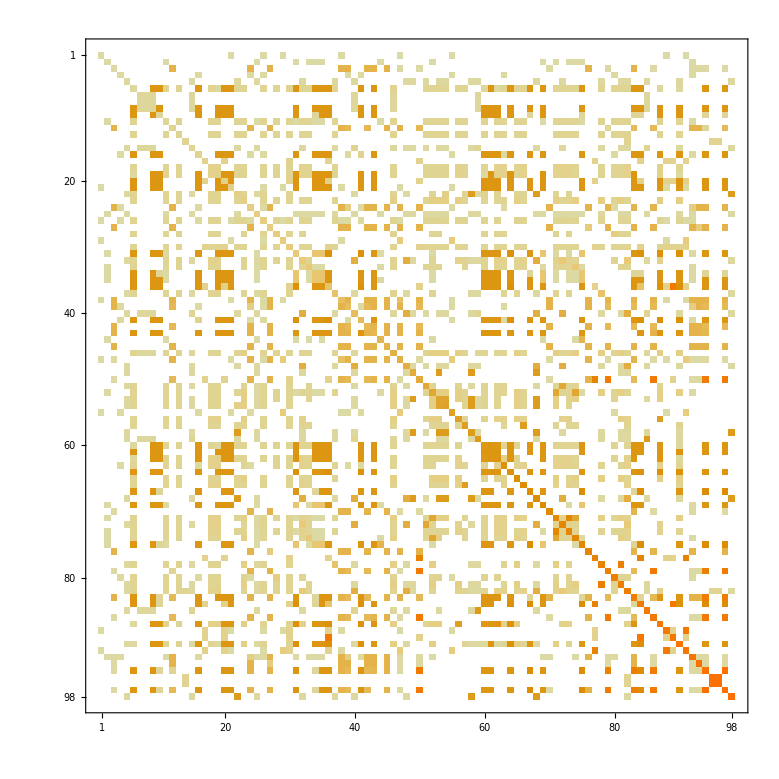

```mathematica
MatrixPlot[M]
```

```mathematica
Partition[Map[Piecewise[{{0, #==0}, {1, #≠0}}]&,Flatten[M],3],29]//MatrixForm
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[M].

Piecewise::argt: Piecewise called with 0 arguments; 1 or 2 arguments are expected.

Piecewise[]

```mathematica
DeleteDuplicates[mm]
Length[%]
```

{8917057,16916545,17041537,17043490,17043521,4726849,8915073,8917026,8536129,16851073,16916514,16910593,17040514,17041444,4472897,2629761,4726818,4720897,8914050,8914980,8470657,8536098,16847105,16818306,16850980,8522241,16909570,17040452,16910376}

29

```mathematica
Table[Flatten[Position[mm,DeleteDuplicates[mm][[j]]]],{j,1,29}]
```

```mathematica
st[list_]:=Map[First[Sort[#,Apply[Plus,IntegerDigits[#1,2]]<Apply[Plus,IntegerDigits[#2,2]]&]]&,list]
```

```mathematica
st[%]
```

```mathematica
aa={1,32,128,64,1024,1152,16,384,2176,513,2304,17,144,2240,1536,288,1664,2082,544,2048,66,2184,1088,194,3073,2336,1089,98,2242};
```

```mathematica
dd=Map[PadLeft[IntegerDigits[#,2],12]&,%]
```

{{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,1,0,0,0,0},{1,0,0,0,1,1,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0},{0,1,1,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,1,0},{0,0,1,0,0,0,1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0},{1,0,0,0,1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,1,0},{1,1,0,0,0,0,0,0,0,0,0,1},{1,0,0,1,0,0,1,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,1,1,0,0,0,1,0},{1,0,0,0,1,1,0,0,0,0,1,0}}

```mathematica
ss=Map[Flatten[Position[#,1]]&,dd]
```

{{12},{7},{5},{6},{2},{2,5},{8},{4,5},{1,5},{3,12},{1,4},{8,12},{5,8},{1,5,6},{2,3},{4,7},{2,3,5},{1,7,11},{3,7},{1},{6,11},{1,5,9},{2,6},{5,6,11},{1,2,12},{1,4,7},{2,6,12},{6,7,11},{1,5,6,11}}

```mathematica
Length[ss]
```

29

```mathematica
Sort[DeleteDuplicates[Flatten[ss]],Less]
```

{1,2,3,4,5,6,7,8,9,11,12}

```mathematica
ss[[10]]
```

{3,12}

```mathematica
M=Partition[Flatten[Table[Piecewise[{{Flatten[Position[ss,ss[[i]]∩ss[[j]]]], Flatten[Position[ss,ss[[i]]∩ss[[j]]]]≠{}}, {{0}, True}}],{i,1,29},{j,1,29}]],29];
M//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0
0 | 0 | 3 | 0 | 0 | 3 | 0 | 3 | 3 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 4 | 0 | 0 | 4 | 4 | 4
0 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 5 | 0 | 5 | 0 | 0
0 | 0 | 3 | 0 | 5 | 6 | 0 | 3 | 3 | 0 | 0 | 0 | 3 | 3 | 5 | 0 | 6 | 0 | 0 | 0 | 0 | 3 | 5 | 3 | 5 | 0 | 5 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 7 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 3 | 0 | 8 | 3 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 3
0 | 0 | 3 | 0 | 0 | 3 | 0 | 3 | 9 | 0 | 20 | 0 | 3 | 9 | 0 | 0 | 3 | 20 | 0 | 20 | 0 | 9 | 0 | 3 | 20 | 20 | 0 | 0 | 9
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 11 | 0 | 0 | 20 | 0 | 0 | 0 | 20 | 0 | 20 | 0 | 20 | 0 | 0 | 20 | 11 | 0 | 0 | 20
1 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 1 | 0 | 12 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 3 | 0 | 0 | 3 | 7 | 3 | 3 | 0 | 0 | 7 | 13 | 3 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 3
0 | 0 | 3 | 4 | 0 | 3 | 0 | 3 | 9 | 0 | 20 | 0 | 3 | 14 | 0 | 0 | 3 | 20 | 0 | 20 | 4 | 9 | 4 | 0 | 20 | 20 | 4 | 4 | 14
0 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 5 | 0 | 5 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 2 | 0
0 | 0 | 3 | 0 | 5 | 6 | 0 | 3 | 3 | 0 | 0 | 0 | 3 | 3 | 15 | 0 | 17 | 0 | 0 | 0 | 0 | 3 | 5 | 3 | 5 | 0 | 5 | 0 | 3
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 20 | 0 | 0 | 20 | 0 | 2 | 0 | 18 | 2 | 20 | 0 | 20 | 0 | 0 | 20 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 20 | 0 | 0 | 20 | 0 | 0 | 0 | 20 | 0 | 20 | 0 | 20 | 0 | 0 | 20 | 20 | 0 | 0 | 20
0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 21 | 0 | 4 | 21 | 0 | 0 | 4 | 21 | 21
0 | 0 | 3 | 0 | 0 | 3 | 0 | 3 | 9 | 0 | 20 | 0 | 3 | 9 | 0 | 0 | 3 | 20 | 0 | 20 | 0 | 22 | 0 | 3 | 20 | 20 | 0 | 0 | 9
0 | 0 | 0 | 4 | 5 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 5 | 0 | 5 | 0 | 0 | 0 | 4 | 0 | 23 | 4 | 5 | 0 | 23 | 4 | 4
0 | 0 | 3 | 4 | 0 | 3 | 0 | 3 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 21 | 3 | 4 | 24 | 0 | 0 | 4 | 21 | 24
1 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 20 | 1 | 20 | 1 | 0 | 20 | 5 | 0 | 5 | 20 | 0 | 20 | 0 | 20 | 5 | 0 | 25 | 20 | 0 | 0 | 20
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 11 | 0 | 0 | 20 | 0 | 16 | 0 | 0 | 2 | 20 | 0 | 20 | 0 | 0 | 20 | 26 | 0 | 2 | 20
1 | 0 | 0 | 4 | 5 | 5 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 4 | 5 | 0 | 5 | 0 | 0 | 0 | 4 | 0 | 23 | 4 | 0 | 0 | 27 | 4 | 4
0 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 2 | 0 | 0 | 2 | 0 | 21 | 0 | 4 | 21 | 0 | 2 | 4 | 28 | 21
0 | 0 | 3 | 4 | 0 | 3 | 0 | 3 | 9 | 0 | 20 | 0 | 3 | 14 | 0 | 0 | 3 | 0 | 0 | 20 | 21 | 9 | 4 | 24 | 20 | 20 | 4 | 21 | 29)

```mathematica
MatrixPlot[M]
```

```mathematica
Partition[Map[Piecewise[{{0, #==0}, {1, #≠0}}]&,Flatten[M],3],29]//MatrixForm
ArrayPlot[%]
```

-Graphics-

```mathematica
SetAttributes[RemainingNonUniformTime,HoldAll];
RemainingNonUniformTime[content_,ticker_,min_,max_,period_]:=Block[{T0=AbsoluteTime[],lstTickerTracker,tickerTracker={}},ticker=min;
Monitor[content,Refresh[lstTickerTracker=AppendTo[tickerTracker,AbsoluteTime[]];
Panel@Grid[{{"Initiated at timestamp:",ToString[DateString[T0]]},{"Current progress:  ",ProgressIndicator[ticker,{min,max}],ticker},{"Avg. Exp. process termination: ",If[Length[lstTickerTracker]>9,ToString[DateString[(T0+(0.5*First@Commonest@Differences@lstTickerTracker/10*(max-min))+(0.5*Max@Differences@Take[lstTickerTracker,-10]/10*(max-min)))]],"Initializing..."]},{"Realtime prediction:  ",If[Length[lstTickerTracker]>9,ToString[DateString[(AbsoluteTime[]+(Mean@Differences@Take[lstTickerTracker,-10]/10)*(max-ticker))]],"Initializing..."]},{"Current timestamp: ",ToString[DateString[AbsoluteTime[]]]}},Alignment->Left],UpdateInterval->period,TrackedSymbols->{}]]]
```

```mathematica
pa[n_]:=Table[Table[1,{i,1,n}]+PadLeft[IntegerDigits[x,n],n],{x,1,n^n-1}]
ta[x_,n_]:=IdentityMatrix[n]+SparseArray[{{x,x+1},{x+1,x},{x,x},{x+1,x+1}}->{1,1,-1,-1},{n,n}]
t[n_]:=Join[{IdentityMatrix[n]},Table[ta[x,n],{x,1,n-1}]]
p[n_]:=Map[t[n][[Delete[#,1]]]&,pa[n]]
f[n_]:=Map[FromDigits[Flatten[#],2]&,Table[Apply[Dot,Delete[p[n][[k]],1]],{k,1,n^n-1}]]
Monitor[Flatten[Map[First,Table[Position[ww,i],{i,DeleteDuplicates[ww]}]]],i]
```

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[ww].

Table::iterb: Iterator {i, DeleteDuplicates[ww]} does not have appropriate bounds.

Table::itform: Argument First[{i, DeleteDuplicates[ww]}] at position 2 does not have the correct form for an iterator.

Table[First[Position[ww,i]],First[{i,DeleteDuplicates[ww]}]]

```mathematica
pa7=Monitor[pa[7],x]
```

{{1,1,1,1,1,1,2},{1,1,1,1,1,1,3},{1,1,1,1,1,1,4},{1,1,1,1,1,1,5},{1,1,1,1,1,1,6},{1,1,1,1,1,1,7},{1,1,1,1,1,2,1},{1,1,1,1,1,2,2},{1,1,1,1,1,2,3},{1,1,1,1,1,2,4},{1,1,1,1,1,2,5},{1,1,1,1,1,2,6},{1,1,1,1,1,2,7},{1,1,1,1,1,3,1},{1,1,1,1,1,3,2},{1,1,1,1,1,3,3},{1,1,1,1,1,3,4},{1,1,1,1,1,3,5},{1,1,1,1,1,3,6},{1,1,1,1,1,3,7},{1,1,1,1,1,4,1},{1,1,1,1,1,4,2},{1,1,1,1,1,4,3},{1,1,1,1,1,4,4},{1,1,1,1,1,4,5},«823492»,{7,7,7,7,7,4,4},{7,7,7,7,7,4,5},{7,7,7,7,7,4,6},{7,7,7,7,7,4,7},{7,7,7,7,7,5,1},{7,7,7,7,7,5,2},{7,7,7,7,7,5,3},{7,7,7,7,7,5,4},{7,7,7,7,7,5,5},{7,7,7,7,7,5,6},{7,7,7,7,7,5,7},{7,7,7,7,7,6,1},{7,7,7,7,7,6,2},{7,7,7,7,7,6,3},{7,7,7,7,7,6,4},{7,7,7,7,7,6,5},{7,7,7,7,7,6,6},{7,7,7,7,7,6,7},{7,7,7,7,7,7,1},{7,7,7,7,7,7,2},{7,7,7,7,7,7,3},{7,7,7,7,7,7,4},{7,7,7,7,7,7,5},{7,7,7,7,7,7,6},{7,7,7,7,7,7,7}}

```mathematica
t7=Monitor[t[7],{x,n}]
```

{{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1}},{{0,1,0,0,0,0,0},{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,1,0,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,0,1,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,1,0,0},{0,0,0,1,0,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,0,1},{0,0,0,0,0,1,0}}}

```mathematica
p7=Map[t7[[Delete[#,1]]]&,pa7]
```

```mathematica
f8=Monitor[Map[FromDigits[Flatten[#],2]&,Table[Apply[Dot,Delete[p8[[k]],1]],{k,1,8^8-1}]],k]
```

```mathematica
ws[x_,y_]:=x+y-x y
```

```mathematica
x/(x-1)==y
```

```mathematica
Reduce[x+y-x y==1,y]
```

x==1||y==1

```mathematica
Reduce[x+x/(x-1)-x^2/(x-1)==0]
```

True

```mathematica
1+y-1y
```

```mathematica
Join[{1,2,3},{3,2,1}]
```

{1,2,3,3,2,1}

```mathematica
t[x_,y_]:=Piecewise[{{Join[P[y][[1]],Floor[x/4]], Table[IntegerDigits[x,2][[DigitCount[x,2]-i]],{i,1,DigitCount[x,2]}]==IntegerDigits[1,2]}, {Join[P[y][[2]],Floor[x/4]], Table[IntegerDigits[x,2][[DigitCount[x,2]-i]],{i,1,DigitCount[x,2]}]==IntegerDigits[2,2]}, {Join[P[y][[3]],Floor[x/4]], Table[IntegerDigits[x,2][[DigitCount[x,2]-i]],{i,1,DigitCount[x,2]}]==IntegerDigits[3,2]}, {., .}, {., .}, {., .}, {Join[P[y][[Length[P[y]]]],Floor[x/4]], Table[IntegerDigits[x,2][[DigitCount[x,2]-i]],{i,1,DigitCount[x,2]}]==IntegerDigits[Length[P[y]],2]}}]
P[y_]:=diff[Flatten[Position[Join[{0},IntegerDigits[y,2]],0]]]-1
```

```mathematica
FromDigits[{0,0,1,1,0,1,1,1,1,0,1,1,1,1,1,1,0,0,0},2]
```

114168

```mathematica
P[114168]
```

{4,6,0,0}

```mathematica
diff[Flatten[{{1},{2},{5},{10},{17},{18},{19}}]]-1
```

{0,2,4,6,0,0}

```mathematica
diff[list_]:=Table[list[[i+1]]-list[[i]],{i,1,Length[list]-1}]
```